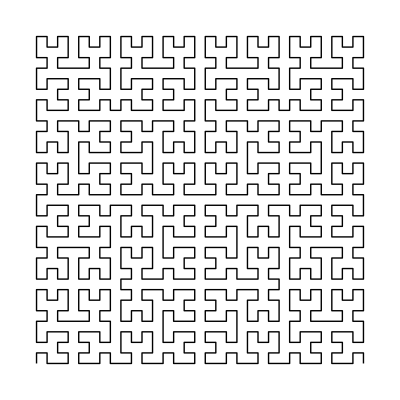
```mathematica
position = {};
count = 0;

Lmove[z_String,Ldelta_]:=Switch[z,"+",Ltheta+=Ldelta;,"-",Ltheta-=Ldelta;,"F",Lpos+={Cos[Ltheta],Sin[Ltheta]},"B",Lpos-={Cos[Ltheta],Sin[Ltheta]},_,Lpos+=0.;
AppendTo[position,Chop[Lpos]];
count++;
];

LSystem::usage="LSystem[axiom, {rules}, n, Ldelta:90 Degree]
    creates the L-string for the nth iteration of
    the list 'rules', starting with the string 'axiom'.";

LSystem[axiom_,rules_List,n_Integer,Ldelta_:N[90 Degree]]:=Nest[StringReplace[#,rules]&,axiom,n];

Off[General::spell1];

LShow[lstring_String,Ldelta_:N[90 Degree]]:=(Lpos={0.,0.};
Ltheta=0.;
Show[Graphics[Line[Prepend[DeleteCases[Map[Lmove[#,Ldelta]&,Characters[lstring]],
Null],{0,0}]]],PlotStyle->Red,AspectRatio->Automatic]);

On[General::spell1];

Show@LSystem["L",(*Hilbert curve*){"L"->"+RF-LFL-FR+","R"->"-LF+RFR+FL-"},3]
imgFrac=-Graphics-;
```

Show::gtype: String is not a type of graphics.

Show[+-+RF-LFL-FR+F+-LF+RFR+FL-F-LF+RFR+FL-+F+RF-LFL-FR+-F-+-LF+RFR+FL-F-+RF-LFL-FR+F+RF-LFL-FR+-F-LF+RFR+FL-+F+-LF+RFR+FL-F-+RF-LFL-FR+F+RF-LFL-FR+-F-LF+RFR+FL-+-F-+RF-LFL-FR+F+-LF+RFR+FL-F-LF+RFR+FL-+F+RF-LFL-FR+-+]

```mathematica
{{□, □}}
```

```mathematica
F[frequency_,t_]:=Sin[frequency 2*100π t]

sounds={};
soundNotes={};
colors={};
aOrdered={};
as={};
freqs={};
size=3;
img=Image[ColorConvert[ImageResize[-Graphics-, {size,size}],"Grayscale"],ImageSize->300];

a=PixelValue[ColorConvert[ImageResize[-Graphics-, {size,size}],"Grayscale"], {All,All}]*10;

For[i=1,i≤size,i++,
	AppendTo[as,a[[i;;;;size]]]]
a=Round[as];
Length[position]
A=Flatten[a];
MatrixForm[a]
For[i=1,i<Length[position],i++,
x=position[[i]][[1]];
y=position[[i]][[2]];
sounds=AppendTo[sounds,a[[x+1]][[y+1]]];
soundNotes=AppendTo[soundNotes,SoundNote[sounds[[i]]]];
aOrdered=AppendTo[aOrdered,SoundNote[A[[i]]]];

freqs=AppendTo[freqs,Play[Chop[F[sounds[[i]],t]],{t,0,6}]];
]

Sound[sounds,{0,2}]
(*Sound[aOrdered,{0,2}]
Sound[soundNotes,{0,2}]*)
Show[{img,imgFrac}]
```

0

(3 | 5 | 3
3 | 6 | 3
2 | 4 | 2)

Sound[{},{0,2}]

-Graphics-